```mathematica
Remove["Global`*"]
```

## Complex Matrix Draw

### ComplexMatrixDraw Code (copy to your Notebook, evaluate and use the ComplexMatrixDraw function)

Introduction: ComplexMatrixDraw daws a rectangular matrix of complex numbers cij as an array of cells, each cell having possibly:
	- a frame and a central point;
	- a 2D shape with an area proportional to |cij| or given by the optional function functionFor2DShapeArea(cij);
	- an arrow with angle arg(cij) and length  |cij| or given by the optional function  functionForArrowLength(cij);
	- a label.
	
Syntax: ComplexMatrixDraw[m,opts] with 
	m: a number, a vector (list of numbers) or a matrix (a list of list of numbers)
	opts: optional replacement rules of the type optionName->optionValue as described below:

Several options (with default behavior) are available:
	
	Option for cell placement. The matrix cell i,j (i=1 to number of lines (top to bottom), j=1 to number of columns (left to rigth) is drawn by default between coordinates j-1 and j for x and  -i+1 and -i+1.5 for y.
		ignoreCell:  function of the position {i,j} returning True or False to decide whether to ignore the ij cell, or to draw it normally. Default is the pure function False & giving always false.
		offset: a list {xOffset,yOffset} (default is {0,0}) indicating how to shift the matrix. 	
	Options for the cell frame:
		- showFrame: True (default) or False. Draw a black square around each matrix cell
		- frameFaceFunction: function of the position {i,j} returning directives for rendering the face of the square frame (default is {White, Opacity[0]}&, i.e. transparent)
		- showCentralPoint: True or False (default) wheter to draw a central point in the cell.
		- centralPointSize: parameter of the PointSize directive (Tiny,Small, Medium, or a relative size like 0.01 for example).
	Options for the 2D shape representing the complex number:
		- show2DShape: True (default) or False. Whether to draw the 2D shape or not.
		- whatShape: "circle" (default) or "square".
		- functionFor2DShapeAera: any  single argument function to be applied to cij to define the area of the 2D shape (default is Abs).
		- hide2DShapeSmallerThan: Value of functionFor2DShapeAera(cij) below which the 2D shape should not be drawn  (default is 0).
		- borderDirectives: graphics directive for the EdgeForm function (color, thickness, type of line, etc): default is {Black, Thickness[0,001]}.
		- fill2DShape: whether to fill the 2Dshape (default is True);
		- fillingColor: Filling color function  f[ |cij| , arg(cij)] of the 2D shape. Default is Hue[#2/(2π)+0.5]&, i.e a cyclic color function of the phase arg(cij) that is cyan for φ=0 and red for φ=π .
	Options for the Arrow representing the complex Number
		- showArrow:  True (default) or False. wheter to draw the arrow or not.
		- functionForArrowLength: any  single argument function to be applied to cij to define the length of the arrow (default is Abs).
		- hideArrowSmallerThan: Value of functionForArrowLength(cij) below which the arrow should not be drawn  (default is 0).
		- arrowDirectives:  graphics directive before the Arrow function (color, thickness, type of line, etc): Default is {Black, Thickness[0.001], Arrowheads[0.05]}
	Options for the label included in the cell
		- showLabel: True or False (default). Whether to write the number in the cell or not.
		- labelFunction: Function to apply to the number to form the label. Default is Identity
		- labelStyle: A directive for Style[], such as Small (default), Medium, Large, Red ...
		- labelShift: a list {Δx,Δy} (default is {0,0}) indicating how to shift the text in the cell.

```mathematica
Options[myPlotElement]=
{ ignoreCell->(False&),offset->{0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
show2DShape->True,whatShape->"circle",functionFor2DShapeAera->Abs,hide2DShapeSmallerThan->0,borderDirectives->{Black,Thickness[0.001]},fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5]&),
showArrow->True,functionForArrowLength->Abs,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}
} ;
myPlotElement[c_,position_,OptionsPattern[]]:=
Block[
{center=position+{-0.5,1.5}+OptionValue[offset],
shapeAera=OptionValue[functionFor2DShapeAera][c],
arrowLength=OptionValue[functionForArrowLength][c],
φ=Arg[c],
frame={},shape={},arrow={},centralPoint={},number={}
},
If[!OptionValue[ignoreCell][position],If[OptionValue[showFrame],frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Rectangle[center-0.5{1,-1},center+0.5{1,-1}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[show2DShape ]&& shapeAera>=OptionValue[hide2DShapeSmallerThan],
shape={EdgeForm[OptionValue[borderDirectives]],If[OptionValue[fill2DShape],FaceForm[OptionValue[fillingColor][Abs[c],φ]],FaceForm[]]};
shape=Append[shape,
Switch[OptionValue[whatShape],
"square",Rectangle[center-Sqrt[shapeAera]/2,center+Sqrt[shapeAera]/2],
_,Disk[center,Sqrt[shapeAera]/2]]]];
If[OptionValue[showArrow] && arrowLength>=OptionValue[hideArrowSmallerThan],
arrow=Append[OptionValue[arrowDirectives],Arrow[{center,center+0.5arrowLength{Cos[φ],Sin[φ]}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics[frame~Join~centralPoint~Join~shape~Join~arrow~Join~centralPoint~Join~number]];
complexMatrixDraw[number_?NumberQ,opts___]:=complexMatrixDraw[{{number}},opts];
complexMatrixDraw[vector_?VectorQ,opts___]:=complexMatrixDraw[List/@vector,opts];
complexMatrixDraw[matrix_,opts___]:=Show[MapIndexed[myPlotElement[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}]];
```

```mathematica
lowerTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]>-#[[2]]&)]
upperTriangleComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]<-#[[2]]&)]
diagonalComplexMatrixDraw[matrix_,opts___]:=complexMatrixDraw[matrix,opts,ignoreCell->(#[[1]]!=-#[[2]]&)]
```

### matrixDraw3D

```mathematica
Options[myPlotElement3D]=
{ ignoreCell->(False&),offset->{0,0,0},
showFrame->True,frameFaceFunction->({White,Opacity[0]}&),showCentralPoint->False,centralPointSize->Small,
showBar->True,whatBarShape->"circle",barLengthFunction->Abs,barDiameter->0.99,hideBarSmallerThan->0,barDirectives->{Opacity[1]},barColorFunction->(Hue[#2/(2π )+0.5]&),
showArrow->True,hideArrowSmallerThan->0,arrowDirectives->{Black,Thickness[0.001],Arrowheads[0.05]},arrowLength->(1/2&),
showLabel->False, labelFunction->Identity, labelStyle->Small,labelShift->{0,0}};

myPlotElement3D[c_,position_,OptionsPattern[]]:=
Block[
{center=Append[position+{-0.5,1.5},0]+OptionValue[offset],φ=Arg[c],frame={},bar={},arrow={},centralPoint={},number={},val=OptionValue[barLengthFunction][c]},
If[!OptionValue[ignoreCell][position],
If[OptionValue[showFrame],
frame={{EdgeForm[Dashed],FaceForm[OptionValue[frameFaceFunction][position[[1]],position[[2]]]],Polygon[{center+{-0.5,-0.5,0},center+{0.5,-0.5,0},center+{0.5,0.5,0},center+{-0.5,0.5,0}}]}}];
If[OptionValue[showCentralPoint],centralPoint={Black,PointSize[OptionValue[centralPointSize]],Point[center]}];
If[OptionValue[showBar] &&Abs[val]>OptionValue[hideBarSmallerThan],
bar=Append[OptionValue[barDirectives],OptionValue[barColorFunction][val,Arg[c]]];
bar=Append[bar,
Switch[OptionValue[whatBarShape],
"square",Cuboid[center-OptionValue[barDiameter]{0.5,0.5,0},center+OptionValue[barDiameter]{0.5,0.5,0}+{0,0,val}],
_,Cylinder[{center,center+{0,0,val}},OptionValue[barDiameter]/2]]]];
If[OptionValue[showArrow] && Abs[val]>OptionValue[hideArrowSmallerThan],
arrow=OptionValue[arrowDirectives];
AppendTo[arrow,Arrow[{center+{0,0,val},center+{0,0,val}+OptionValue[arrowLength][val]{ Cos[Arg[c]], Sin[Arg[c]],0}}]]];
If[OptionValue[showLabel],number={Text[Style[OptionValue[labelFunction][c],OptionValue[labelStyle]],center+OptionValue[labelShift]]}];
];
Graphics3D[frame~Join~centralPoint~Join~bar~Join~arrow~Join~centralPoint~Join~number,Lighting->{{"Ambient",White}}]];

matrixDraw3D[number_?NumberQ,opts___]:=matrixDraw3D[{{number}},opts];
matrixDraw3D[vector_?VectorQ,opts___]:=matrixDraw3D[List/@vector,opts];
matrixDraw3D[matrix_,opts___]:=Show[MapIndexed[myPlotElement3D[#1,Reverse[#2]{1,-1},opts]&,matrix,{2}],BoxRatios->{1,1,1}];
```

```mathematica
t = TransformationMatrix[RotationTransform[π/4,{1,0,0}].RotationTransform[π/4,{0,0,1}].RescalingTransform[{{-0.1,4.1},{-0.1,4.1},{-0.1,1.1}}]];
p = {{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,2}};
tomoMatrices=Map[matrixDraw3D[#,whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},barDiameter->0.5,arrowLength->(0.3&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&),barColorFunction->(RGBColor[Cos[#2/2]^2,Sin[#2]/2+0.5,1.0-Cos[#2/2]^2]&)]&,tomos5];
```

```mathematica
Show[#,ViewPoint->10000{1.1,-1.1,1.5},BoxRatios->{1,1,0.5}]&/@tomoMatrices
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

# Grover FOC5-3rd run

### Density matrices Grover

#### Density matrix as a function of Pauli Set

```mathematica
Clear[x,y,z,i];
opBase1={x,y,z,i};
opBase2=Outer[KroneckerProduct,opBase1,opBase1]//Flatten
rule1=(KroneckerProduct[op1_,op2_]:>ToExpression[ToString[op1]<>ToString[op2]]);
pauliSet=opBase2/.rule1; "Pauli set is "<>ToString[pauliSet]
x={{0,1},{1,0}};y={{0,-ⅈ},{ⅈ,0}};z={{1,0},{0,-1}};i={{1,0},{0,1}};
ρM=Table[ρ[i,j],{i,4},{j,4}];
pauliSetTh=FullSimplify[Tr[#.ρM]&/@opBase2];
sys=#==0&/@(pauliSet-pauliSetTh);
ρS=ρM/.(Solve[sys,ρM//Flatten]//Flatten);
"ρS="MatrixForm[ρS]
Clear[x,y,z,i];
```

{KroneckerProduct[x,x],KroneckerProduct[x,y],KroneckerProduct[x,z],KroneckerProduct[x,i],KroneckerProduct[y,x],KroneckerProduct[y,y],KroneckerProduct[y,z],KroneckerProduct[y,i],KroneckerProduct[z,x],KroneckerProduct[z,y],KroneckerProduct[z,z],KroneckerProduct[z,i],KroneckerProduct[i,x],KroneckerProduct[i,y],KroneckerProduct[i,z],KroneckerProduct[i,i]}

Pauli set is {xx, xy, xz, xi, yx, yy, yz, yi, zx, zy, zz, zi, ix, iy, iz, ii}

ρS= (1/4 (ii+iz+zi+zz) | 1/4 (ix-ⅈ iy+zx-ⅈ zy) | 1/4 (xi+xz-ⅈ yi-ⅈ yz) | 1/4 (xx-ⅈ xy-ⅈ yx-yy)
1/4 (ix+ⅈ iy+zx+ⅈ zy) | 1/4 (ii-iz+zi-zz) | 1/4 (xx+ⅈ xy-ⅈ yx+yy) | 1/4 (xi-xz-ⅈ yi+ⅈ yz)
1/4 (xi+xz+ⅈ yi+ⅈ yz) | 1/4 (xx-ⅈ xy+ⅈ yx+yy) | 1/4 (ii+iz-zi-zz) | 1/4 (ix-ⅈ iy-zx+ⅈ zy)
1/4 (xx+ⅈ xy+ⅈ yx-yy) | 1/4 (xi-xz+ⅈ yi-ⅈ yz) | 1/4 (ix+ⅈ iy-zx-ⅈ zy) | 1/4 (ii-iz-zi+zz))

```mathematica
ρM
pauliSet
```

{{{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[1,1],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[1,2],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[1,3],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[1,4]},{{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[2,1],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[2,2],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[2,3],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[2,4]},{{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[3,1],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[3,2],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[3,3],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[3,4]},{{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[4,1],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[4,2],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[4,3],{{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}}[4,4]}}

{xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii}

```mathematica
ρ={{ρ11,ρ12,ρ13,ρ14},{ρ21,ρ22,ρ23,ρ24},{ρ31,ρ32,ρ33,ρ34},{ρ41,ρ42,ρ43,ρ44}};
meas={xx,xy,xz,xi,yx,yy,yz,yi,zx,zy,zz,zi,ix,iy,iz,ii};
σx={{0,1},{1,0}};
σy={{0,-ⅈ},{ⅈ,0}};
σz={{1,0},{0,-1}};
id={{1,0},{0,1}};
measure=FullSimplify[Tr[#.ρ]&/@opBase2];
```

#### Ideal density matrices

```mathematica
idealStates3=Table[(-1)^KroneckerDelta[i,j],{i,1,4},{j,1,4}]/2;
idealStates5=Table[KroneckerDelta[i,j],{i,1,4},{j,1,4}];
MatrixForm/@(idealMatrices3=KroneckerProduct[#,#]&/@idealStates3)
MatrixForm/@(idealMatrices5=KroneckerProduct[#,#]&/@idealStates5)
opts0={
borderColor->Black,arrowColor->Black,fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&), thicknessShape->0.004, thicknessArrow->0.003,frameFaceFunction->(GrayLevel[1-0.05KroneckerDelta[#1,-#2]]&),
showCentralPoint->True ,centralPointSize->Medium};
opts0b={
borderColor->Black,arrowColor->Black,fill2DShape->True,fillingColor->(Hue[#2/(2π)+0.5,0.2,1]&),hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&), thicknessShape->0.004, thicknessArrow->0.003,frameFaceFunction->(GrayLevel[1-0.05KroneckerDelta[#1,-#2]]&),
showCentralPoint->True ,centralPointSize->Medium};
idealGraphs3=ComplexMatrixDraw[#,Sequence @@ opts0]&/@idealMatrices3
idealGraphs5=ComplexMatrixDraw[#,Sequence @@ opts0]&/@idealMatrices5
```

{(1/4 | -1/4 | -1/4 | -1/4
-1/4 | 1/4 | 1/4 | 1/4
-1/4 | 1/4 | 1/4 | 1/4
-1/4 | 1/4 | 1/4 | 1/4),(1/4 | -1/4 | 1/4 | 1/4
-1/4 | 1/4 | -1/4 | -1/4
1/4 | -1/4 | 1/4 | 1/4
1/4 | -1/4 | 1/4 | 1/4),(1/4 | 1/4 | -1/4 | 1/4
1/4 | 1/4 | -1/4 | 1/4
-1/4 | -1/4 | 1/4 | -1/4
1/4 | 1/4 | -1/4 | 1/4),(1/4 | 1/4 | 1/4 | -1/4
1/4 | 1/4 | 1/4 | -1/4
1/4 | 1/4 | 1/4 | -1/4
-1/4 | -1/4 | -1/4 | 1/4)}

{(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)}

{ComplexMatrixDraw[{{1/4,-1/4,-1/4,-1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{1/4,-1/4,1/4,1/4},{-1/4,1/4,-1/4,-1/4},{1/4,-1/4,1/4,1/4},{1/4,-1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{1/4,1/4,-1/4,1/4},{1/4,1/4,-1/4,1/4},{-1/4,-1/4,1/4,-1/4},{1/4,1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{-1/4,-1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium]}

{ComplexMatrixDraw[{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium]}

```mathematica
idealGraphs3b=ComplexMatrixDraw[#,Sequence @@ opts0b]&/@idealMatrices3
idealGraphs5b=ComplexMatrixDraw[#,Sequence @@ opts0b]&/@idealMatrices5
```

{ComplexMatrixDraw[{{1/4,-1/4,-1/4,-1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{1/4,-1/4,1/4,1/4},{-1/4,1/4,-1/4,-1/4},{1/4,-1/4,1/4,1/4},{1/4,-1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{1/4,1/4,-1/4,1/4},{1/4,1/4,-1/4,1/4},{-1/4,-1/4,1/4,-1/4},{1/4,1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{-1/4,-1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium]}

{ComplexMatrixDraw[{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium]}

```mathematica
matrixDraw3D[idealStates3,whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},barDiameter->0.5,arrowLength->(0.1&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&),barColorFunction->(Hue[#2/(2π )+0.5,0.5,1]&)]
```

-Graphics3D-

```mathematica
Show[%136,BoxRatios->{1,1,0.5}]
```

Show::gtype: Symbol is not a type of graphics.

Show[Null,BoxRatios→{1,1,0.5}]

#### Import measured density matrices

```mathematica
replacements={"j"->"ⅈ","e"->"*10^"};
myImport[fileName_,type_,headerLines_:0,printHeader_:False]:=
Block[
{data=Import[fileName,type],depth},
depth=data//dimensions//Length;
If[printHeader,Print["Header: "<>ToString[Take[data,headerLines]]]];
data=(Map[StringReplace[#,replacements]&,Drop[data,headerLines],{depth}])// ToExpression
]
```

```mathematica
data=myImport["L:\\local-expdata\\2 Qubit Experiments\\FO-C5\\3rd-Run\\2011_04_21\\good_data\\Grover Search Algorithm-1-density matrices-20.txt","Table",1,True];
```

Header: {{state, step, 0, 1, 2, 3, 10, 11, 12, 13, 20, 21, 22, 23, 30, 31, 32, 33}}

```mathematica
tomos3=Partition[Drop[#,2],4]&/@Select[data,#[[2]]==3&];
tomos5=Partition[Drop[#,2],4]&/@Select[data,#[[2]]==5&];
tomos3={tomos3[[1]],tomos3[[3]],tomos3[[2]],tomos3[[4]]};
tomos5={tomos5[[1]],tomos5[[3]],tomos5[[2]],tomos5[[4]]};
MatrixForm/@tomos3;
MatrixForm/@tomos5;
opts1={
drawFrame->False,borderColor->Red,arrowColor->Red,fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&), thicknessShape->0.002, thicknessArrow->0.002,frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)};
opts1b={
drawFrame->False,borderColor->RGBColor[1,0,0],arrowColor->RGBColor[1,0,0],fill2DShape->False,hide2DShapeSmallerThan->0.01,arrowSize->0,hideArrowSmallerThan->.01^0.5,functionForArrowLength->(Abs[#]^0.5&), thicknessShape->0.002, thicknessArrow->0.002,frameFaceFunction->(GrayLevel[1-0.1KroneckerDelta[#1,-#2]]&)};
tomoGraphs3=ComplexMatrixDraw[#,Sequence @@ opts1]&/@tomos3
tomoGraphs5=ComplexMatrixDraw[#,Sequence @@ opts1]&/@tomos5
tomoGraphs3b=ComplexMatrixDraw[#,Sequence @@ opts1b]&/@tomos3
tomoGraphs5b=ComplexMatrixDraw[#,Sequence @@ opts1b]&/@tomos5
```

{ComplexMatrixDraw[{{0.365043,-0.239426-0.0793219 ⅈ,-0.201094-0.0658382 ⅈ,-0.227086+0.0075136 ⅈ},{-0.239426+0.0793219 ⅈ,0.236068,0.169927+0.0496018 ⅈ,0.200049},{-0.201094+0.0658382 ⅈ,0.169927-0.0496018 ⅈ,0.229363,0.196727+0.0126711 ⅈ},{-0.227086-0.0075136 ⅈ,0.200049,0.196727-0.0126711 ⅈ,0.169526}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.365796,-0.212979-0.1324 ⅈ,0.168319+0.118436 ⅈ,0.138171+0.148801 ⅈ},{-0.212979+0.1324 ⅈ,0.226219,-0.191912-0.00408204 ⅈ,-0.206345-0.0153204 ⅈ},{0.168319-0.118436 ⅈ,-0.191912+0.00408204 ⅈ,0.213019,0.19161+0.049816 ⅈ},{0.138171-0.148801 ⅈ,-0.206345+0.0153204 ⅈ,0.19161-0.049816 ⅈ,0.194965}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.298423,0.217411+0.0643156 ⅈ,-0.220185-0.0707418 ⅈ,0.171705-0.0172273 ⅈ},{0.217411-0.0643156 ⅈ,0.257396,-0.206667-0.026796 ⅈ,0.177515-0.0510065 ⅈ},{-0.220185+0.0707418 ⅈ,-0.206667+0.026796 ⅈ,0.309022,-0.193571+0.03757 ⅈ},{0.171705+0.0172273 ⅈ,0.177515+0.0510065 ⅈ,-0.193571-0.03757 ⅈ,0.13516}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.327975,0.204059+0.135264 ⅈ,0.179266+0.124587 ⅈ,-0.138489-0.142795 ⅈ},{0.204059-0.135264 ⅈ,0.252411,0.230309+0.0321577 ⅈ,-0.201038-0.000159557 ⅈ},{0.179266-0.124587 ⅈ,0.230309-0.0321577 ⅈ,0.254066,-0.1875-0.0139388 ⅈ},{-0.138489+0.142795 ⅈ,-0.201038+0.000159557 ⅈ,-0.1875+0.0139388 ⅈ,0.165548}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]}

{ComplexMatrixDraw[{{0.698739,-0.0529229+0.146873 ⅈ,-0.0572737+0.0879441 ⅈ,-0.00559644-0.0102862 ⅈ},{-0.0529229-0.146873 ⅈ,0.112203,0.108175,-0.0337102+0.037264 ⅈ},{-0.0572737-0.0879441 ⅈ,0.108175,0.104292,0.00925411+0.0620765 ⅈ},{-0.00559644+0.0102862 ⅈ,-0.0337102-0.037264 ⅈ,0.00925411-0.0620765 ⅈ,0.0847662}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.146931,-0.0994704+0.163872 ⅈ,-0.0200816+0.0463506 ⅈ,-0.0814302-0.00953309 ⅈ},{-0.0994704-0.163872 ⅈ,0.622691,-0.00672935-0.0326438 ⅈ,0.10083+0.0871936 ⅈ},{-0.0200816-0.0463506 ⅈ,-0.00672935+0.0326438 ⅈ,0.0770402,0.108688},{-0.0814302+0.00953309 ⅈ,0.10083-0.0871936 ⅈ,0.108688,0.153338}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.104111,0.0990267,-0.0876516+0.0354145 ⅈ,-0.0400719-0.0245154 ⅈ},{0.0990267,0.0941909,0.0563279+0.0398886 ⅈ,0.112228},{-0.0876516-0.0354145 ⅈ,0.0563279-0.0398886 ⅈ,0.667979,-0.0011507+0.219182 ⅈ},{-0.0400719+0.0245154 ⅈ,0.112228,-0.0011507-0.219182 ⅈ,0.133719}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.0899727,0.00510542+0.0700425 ⅈ,-0.0154056+0.0238865 ⅈ,-0.0201146+0.0412613 ⅈ},{0.00510542-0.0700425 ⅈ,0.182052,0.0409938+0.0145898 ⅈ,-0.122611+0.172242 ⅈ},{-0.0154056-0.0238865 ⅈ,0.0409938-0.0145898 ⅈ,0.0644887,0.0187209+0.0885988 ⅈ},{-0.0201146-0.0412613 ⅈ,-0.122611-0.172242 ⅈ,0.0187209-0.0885988 ⅈ,0.663486}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]}

{ComplexMatrixDraw[{{0.365043,-0.239426-0.0793219 ⅈ,-0.201094-0.0658382 ⅈ,-0.227086+0.0075136 ⅈ},{-0.239426+0.0793219 ⅈ,0.236068,0.169927+0.0496018 ⅈ,0.200049},{-0.201094+0.0658382 ⅈ,0.169927-0.0496018 ⅈ,0.229363,0.196727+0.0126711 ⅈ},{-0.227086-0.0075136 ⅈ,0.200049,0.196727-0.0126711 ⅈ,0.169526}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.365796,-0.212979-0.1324 ⅈ,0.168319+0.118436 ⅈ,0.138171+0.148801 ⅈ},{-0.212979+0.1324 ⅈ,0.226219,-0.191912-0.00408204 ⅈ,-0.206345-0.0153204 ⅈ},{0.168319-0.118436 ⅈ,-0.191912+0.00408204 ⅈ,0.213019,0.19161+0.049816 ⅈ},{0.138171-0.148801 ⅈ,-0.206345+0.0153204 ⅈ,0.19161-0.049816 ⅈ,0.194965}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.298423,0.217411+0.0643156 ⅈ,-0.220185-0.0707418 ⅈ,0.171705-0.0172273 ⅈ},{0.217411-0.0643156 ⅈ,0.257396,-0.206667-0.026796 ⅈ,0.177515-0.0510065 ⅈ},{-0.220185+0.0707418 ⅈ,-0.206667+0.026796 ⅈ,0.309022,-0.193571+0.03757 ⅈ},{0.171705+0.0172273 ⅈ,0.177515+0.0510065 ⅈ,-0.193571-0.03757 ⅈ,0.13516}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.327975,0.204059+0.135264 ⅈ,0.179266+0.124587 ⅈ,-0.138489-0.142795 ⅈ},{0.204059-0.135264 ⅈ,0.252411,0.230309+0.0321577 ⅈ,-0.201038-0.000159557 ⅈ},{0.179266-0.124587 ⅈ,0.230309-0.0321577 ⅈ,0.254066,-0.1875-0.0139388 ⅈ},{-0.138489+0.142795 ⅈ,-0.201038+0.000159557 ⅈ,-0.1875+0.0139388 ⅈ,0.165548}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]}

{ComplexMatrixDraw[{{0.698739,-0.0529229+0.146873 ⅈ,-0.0572737+0.0879441 ⅈ,-0.00559644-0.0102862 ⅈ},{-0.0529229-0.146873 ⅈ,0.112203,0.108175,-0.0337102+0.037264 ⅈ},{-0.0572737-0.0879441 ⅈ,0.108175,0.104292,0.00925411+0.0620765 ⅈ},{-0.00559644+0.0102862 ⅈ,-0.0337102-0.037264 ⅈ,0.00925411-0.0620765 ⅈ,0.0847662}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.146931,-0.0994704+0.163872 ⅈ,-0.0200816+0.0463506 ⅈ,-0.0814302-0.00953309 ⅈ},{-0.0994704-0.163872 ⅈ,0.622691,-0.00672935-0.0326438 ⅈ,0.10083+0.0871936 ⅈ},{-0.0200816-0.0463506 ⅈ,-0.00672935+0.0326438 ⅈ,0.0770402,0.108688},{-0.0814302+0.00953309 ⅈ,0.10083-0.0871936 ⅈ,0.108688,0.153338}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.104111,0.0990267,-0.0876516+0.0354145 ⅈ,-0.0400719-0.0245154 ⅈ},{0.0990267,0.0941909,0.0563279+0.0398886 ⅈ,0.112228},{-0.0876516-0.0354145 ⅈ,0.0563279-0.0398886 ⅈ,0.667979,-0.0011507+0.219182 ⅈ},{-0.0400719+0.0245154 ⅈ,0.112228,-0.0011507-0.219182 ⅈ,0.133719}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)],ComplexMatrixDraw[{{0.0899727,0.00510542+0.0700425 ⅈ,-0.0154056+0.0238865 ⅈ,-0.0201146+0.0412613 ⅈ},{0.00510542-0.0700425 ⅈ,0.182052,0.0409938+0.0145898 ⅈ,-0.122611+0.172242 ⅈ},{-0.0154056-0.0238865 ⅈ,0.0409938-0.0145898 ⅈ,0.0644887,0.0187209+0.0885988 ⅈ},{-0.0201146-0.0412613 ⅈ,-0.122611-0.172242 ⅈ,0.0187209-0.0885988 ⅈ,0.663486}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]}

```mathematica
Map[matrixDraw3D[#,whatBarShape->"square",barDirectives->{Opacity[1]},arrowDirectives->{Opacity[0.8],Red,Thickness[0.005],Arrowheads[0]},barDiameter->0.5,arrowLength->(0.1&),frameFaceFunction->(GrayLevel[1-0.2KroneckerDelta[#1,-#2]]&),barColorFunction->(Hue[#2/(2π )+0.5,0.5,1]&)]&,tomos3]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
graphs3=MapThread[Show[#1,#2]&,{idealGraphs3,tomoGraphs3}];
graphs5=MapThread[Show[#1,#2]&,{idealGraphs5,tomoGraphs5}];
Transpose[{graphs3,graphs5}]//MatrixForm
```

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1/4, -1/4, -1/4, -1/4}, {-1/4, 1/4, 1/4, 1/4}, {-1/4, 1/4, 1/4, 1/4}, {-1/4, 1/4, 1/4, 1/4}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → False, hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 »]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1/4, -1/4, 1/4, 1/4}, {-1/4, 1/4, -1/4, -1/4}, {1/4, -1/4, 1/4, 1/4}, {1/4, -1/4, 1/4, 1/4}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → False, hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 »]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1/4, 1/4, -1/4, 1/4}, {1/4, 1/4, -1/4, 1/4}, {-1/4, -1/4, 1/4, -1/4}, {1/4, 1/4, -1/4, 1/4}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → False, hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[{« 1 »}, drawFrame → False, borderColor → RGBColor[1, 0, 0], arrowColor → RGBColor[1, 0, 0], « 4 », « 22 » → (« 1 »^« 4 » &), thicknessShape → 0.002`, thicknessArrow → 0.002`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &)]].

General::stop: Further output of Show will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → False, hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[{{0.698738990524`, -0.0529228974947` + 0.146872965699` ⅈ, -0.0572737410171` + 0.0879441431465` ⅈ, -0.00559644491333` - 0.0102861771924` ⅈ}, {« 1 »}, {« 1 »}, {-0.00559644491333` + 0.0102861771924` ⅈ, « 2 », 0.0847662027806`}}, « 10 », « 1 »]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → False, hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 »]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → False, hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 », drawFrame → False, borderColor → RGBColor[1, 0, 0], arrowColor → RGBColor[1, 0, 0], « 4 », functionForArrowLength → (« 1 »^0.5` &), thicknessShape → 0.002`, thicknessArrow → 0.002`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &)]].

General::stop: Further output of Show will be suppressed during this calculation.

(Show[ComplexMatrixDraw[{{1/4,-1/4,-1/4,-1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.365043,-0.239426-0.0793219 ⅈ,-0.201094-0.0658382 ⅈ,-0.227086+0.0075136 ⅈ},{-0.239426+0.0793219 ⅈ,0.236068,0.169927+0.0496018 ⅈ,0.200049},{-0.201094+0.0658382 ⅈ,0.169927-0.0496018 ⅈ,0.229363,0.196727+0.0126711 ⅈ},{-0.227086-0.0075136 ⅈ,0.200049,0.196727-0.0126711 ⅈ,0.169526}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.698739,-0.0529229+0.146873 ⅈ,-0.0572737+0.0879441 ⅈ,-0.00559644-0.0102862 ⅈ},{-0.0529229-0.146873 ⅈ,0.112203,0.108175,-0.0337102+0.037264 ⅈ},{-0.0572737-0.0879441 ⅈ,0.108175,0.104292,0.00925411+0.0620765 ⅈ},{-0.00559644+0.0102862 ⅈ,-0.0337102-0.037264 ⅈ,0.00925411-0.0620765 ⅈ,0.0847662}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]]
Show[ComplexMatrixDraw[{{1/4,-1/4,1/4,1/4},{-1/4,1/4,-1/4,-1/4},{1/4,-1/4,1/4,1/4},{1/4,-1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.365796,-0.212979-0.1324 ⅈ,0.168319+0.118436 ⅈ,0.138171+0.148801 ⅈ},{-0.212979+0.1324 ⅈ,0.226219,-0.191912-0.00408204 ⅈ,-0.206345-0.0153204 ⅈ},{0.168319-0.118436 ⅈ,-0.191912+0.00408204 ⅈ,0.213019,0.19161+0.049816 ⅈ},{0.138171-0.148801 ⅈ,-0.206345+0.0153204 ⅈ,0.19161-0.049816 ⅈ,0.194965}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.146931,-0.0994704+0.163872 ⅈ,-0.0200816+0.0463506 ⅈ,-0.0814302-0.00953309 ⅈ},{-0.0994704-0.163872 ⅈ,0.622691,-0.00672935-0.0326438 ⅈ,0.10083+0.0871936 ⅈ},{-0.0200816-0.0463506 ⅈ,-0.00672935+0.0326438 ⅈ,0.0770402,0.108688},{-0.0814302+0.00953309 ⅈ,0.10083-0.0871936 ⅈ,0.108688,0.153338}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]]
Show[ComplexMatrixDraw[{{1/4,1/4,-1/4,1/4},{1/4,1/4,-1/4,1/4},{-1/4,-1/4,1/4,-1/4},{1/4,1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.298423,0.217411+0.0643156 ⅈ,-0.220185-0.0707418 ⅈ,0.171705-0.0172273 ⅈ},{0.217411-0.0643156 ⅈ,0.257396,-0.206667-0.026796 ⅈ,0.177515-0.0510065 ⅈ},{-0.220185+0.0707418 ⅈ,-0.206667+0.026796 ⅈ,0.309022,-0.193571+0.03757 ⅈ},{0.171705+0.0172273 ⅈ,0.177515+0.0510065 ⅈ,-0.193571-0.03757 ⅈ,0.13516}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.104111,0.0990267,-0.0876516+0.0354145 ⅈ,-0.0400719-0.0245154 ⅈ},{0.0990267,0.0941909,0.0563279+0.0398886 ⅈ,0.112228},{-0.0876516-0.0354145 ⅈ,0.0563279-0.0398886 ⅈ,0.667979,-0.0011507+0.219182 ⅈ},{-0.0400719+0.0245154 ⅈ,0.112228,-0.0011507-0.219182 ⅈ,0.133719}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]]
Show[ComplexMatrixDraw[{{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{-1/4,-1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.327975,0.204059+0.135264 ⅈ,0.179266+0.124587 ⅈ,-0.138489-0.142795 ⅈ},{0.204059-0.135264 ⅈ,0.252411,0.230309+0.0321577 ⅈ,-0.201038-0.000159557 ⅈ},{0.179266-0.124587 ⅈ,0.230309-0.0321577 ⅈ,0.254066,-0.1875-0.0139388 ⅈ},{-0.138489+0.142795 ⅈ,-0.201038+0.000159557 ⅈ,-0.1875+0.0139388 ⅈ,0.165548}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.0899727,0.00510542+0.0700425 ⅈ,-0.0154056+0.0238865 ⅈ,-0.0201146+0.0412613 ⅈ},{0.00510542-0.0700425 ⅈ,0.182052,0.0409938+0.0145898 ⅈ,-0.122611+0.172242 ⅈ},{-0.0154056-0.0238865 ⅈ,0.0409938-0.0145898 ⅈ,0.0644887,0.0187209+0.0885988 ⅈ},{-0.0201146-0.0412613 ⅈ,-0.122611-0.172242 ⅈ,0.0187209-0.0885988 ⅈ,0.663486}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]])

```mathematica
graphs3b=MapThread[Show[#1,#2]&,{idealGraphs3b,tomoGraphs3b}];
graphs5b=MapThread[Show[#1,#2]&,{idealGraphs5b,tomoGraphs5b}];
Transpose[{graphs3b,graphs5b}]//MatrixForm
```

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1/4, -1/4, -1/4, -1/4}, {-1/4, 1/4, 1/4, 1/4}, {-1/4, 1/4, 1/4, 1/4}, {-1/4, 1/4, 1/4, 1/4}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → True, fillingColor → (Hue[Slot[« 1 »] Power[« 2 »] + 0.5`, 0.2`, 1] &), hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 »]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1/4, -1/4, 1/4, 1/4}, {-1/4, 1/4, -1/4, -1/4}, {1/4, -1/4, 1/4, 1/4}, {1/4, -1/4, 1/4, 1/4}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → True, fillingColor → (Hue[Slot[« 1 »] Power[« 2 »] + 0.5`, 0.2`, 1] &), hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[{{0.365796011941`, -0.212978718381` - 0.132399540286` ⅈ, 0.168319162588`  + 0.118436025002` ⅈ, 0.138170714919`  + 0.148801009942` ⅈ}, « 3 »}, « 10 », « 1 »]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1/4, 1/4, -1/4, 1/4}, {1/4, 1/4, -1/4, 1/4}, {-1/4, -1/4, 1/4, -1/4}, {1/4, 1/4, -1/4, 1/4}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → True, fillingColor → (Hue[Slot[« 1 »] Power[« 2 »] + 0.5`, 0.2`, 1] &), hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 »]].

General::stop: Further output of Show will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{1, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → True, fillingColor → (Hue[Slot[« 1 »] Power[« 2 »] + 0.5`, 0.2`, 1] &), hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 »]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → True, fillingColor → (Hue[Slot[« 1 »] Power[« 2 »] + 0.5`, 0.2`, 1] &), hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 », drawFrame → False, borderColor → RGBColor[1, 0, 0], arrowColor → « 1 », « 5 », thicknessShape → 0.002`, thicknessArrow → 0.002`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &)]].

Show::gcomb: Could not combine the graphics objects in Show[ComplexMatrixDraw[{{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}}, borderColor → GrayLevel[0], arrowColor → GrayLevel[0], fill2DShape → True, fillingColor → (Hue[Slot[« 1 »] Power[« 2 »] + 0.5`, 0.2`, 1] &), hide2DShapeSmallerThan → 0.01`, arrowSize → 0, hideArrowSmallerThan → 0.1`, functionForArrowLength → (Abs[#1]^0.5` &), thicknessShape → 0.004`, thicknessArrow → 0.003`, frameFaceFunction → (GrayLevel[1 - Times[« 2 »]] &), showCentralPoint → True, centralPointSize → Medium], ComplexMatrixDraw[« 1 »]].

General::stop: Further output of Show will be suppressed during this calculation.

(Show[ComplexMatrixDraw[{{1/4,-1/4,-1/4,-1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4},{-1/4,1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.365043,-0.239426-0.0793219 ⅈ,-0.201094-0.0658382 ⅈ,-0.227086+0.0075136 ⅈ},{-0.239426+0.0793219 ⅈ,0.236068,0.169927+0.0496018 ⅈ,0.200049},{-0.201094+0.0658382 ⅈ,0.169927-0.0496018 ⅈ,0.229363,0.196727+0.0126711 ⅈ},{-0.227086-0.0075136 ⅈ,0.200049,0.196727-0.0126711 ⅈ,0.169526}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.698739,-0.0529229+0.146873 ⅈ,-0.0572737+0.0879441 ⅈ,-0.00559644-0.0102862 ⅈ},{-0.0529229-0.146873 ⅈ,0.112203,0.108175,-0.0337102+0.037264 ⅈ},{-0.0572737-0.0879441 ⅈ,0.108175,0.104292,0.00925411+0.0620765 ⅈ},{-0.00559644+0.0102862 ⅈ,-0.0337102-0.037264 ⅈ,0.00925411-0.0620765 ⅈ,0.0847662}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]]
Show[ComplexMatrixDraw[{{1/4,-1/4,1/4,1/4},{-1/4,1/4,-1/4,-1/4},{1/4,-1/4,1/4,1/4},{1/4,-1/4,1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.365796,-0.212979-0.1324 ⅈ,0.168319+0.118436 ⅈ,0.138171+0.148801 ⅈ},{-0.212979+0.1324 ⅈ,0.226219,-0.191912-0.00408204 ⅈ,-0.206345-0.0153204 ⅈ},{0.168319-0.118436 ⅈ,-0.191912+0.00408204 ⅈ,0.213019,0.19161+0.049816 ⅈ},{0.138171-0.148801 ⅈ,-0.206345+0.0153204 ⅈ,0.19161-0.049816 ⅈ,0.194965}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.146931,-0.0994704+0.163872 ⅈ,-0.0200816+0.0463506 ⅈ,-0.0814302-0.00953309 ⅈ},{-0.0994704-0.163872 ⅈ,0.622691,-0.00672935-0.0326438 ⅈ,0.10083+0.0871936 ⅈ},{-0.0200816-0.0463506 ⅈ,-0.00672935+0.0326438 ⅈ,0.0770402,0.108688},{-0.0814302+0.00953309 ⅈ,0.10083-0.0871936 ⅈ,0.108688,0.153338}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]]
Show[ComplexMatrixDraw[{{1/4,1/4,-1/4,1/4},{1/4,1/4,-1/4,1/4},{-1/4,-1/4,1/4,-1/4},{1/4,1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.298423,0.217411+0.0643156 ⅈ,-0.220185-0.0707418 ⅈ,0.171705-0.0172273 ⅈ},{0.217411-0.0643156 ⅈ,0.257396,-0.206667-0.026796 ⅈ,0.177515-0.0510065 ⅈ},{-0.220185+0.0707418 ⅈ,-0.206667+0.026796 ⅈ,0.309022,-0.193571+0.03757 ⅈ},{0.171705+0.0172273 ⅈ,0.177515+0.0510065 ⅈ,-0.193571-0.03757 ⅈ,0.13516}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.104111,0.0990267,-0.0876516+0.0354145 ⅈ,-0.0400719-0.0245154 ⅈ},{0.0990267,0.0941909,0.0563279+0.0398886 ⅈ,0.112228},{-0.0876516-0.0354145 ⅈ,0.0563279-0.0398886 ⅈ,0.667979,-0.0011507+0.219182 ⅈ},{-0.0400719+0.0245154 ⅈ,0.112228,-0.0011507-0.219182 ⅈ,0.133719}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]]
Show[ComplexMatrixDraw[{{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{1/4,1/4,1/4,-1/4},{-1/4,-1/4,-1/4,1/4}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.327975,0.204059+0.135264 ⅈ,0.179266+0.124587 ⅈ,-0.138489-0.142795 ⅈ},{0.204059-0.135264 ⅈ,0.252411,0.230309+0.0321577 ⅈ,-0.201038-0.000159557 ⅈ},{0.179266-0.124587 ⅈ,0.230309-0.0321577 ⅈ,0.254066,-0.1875-0.0139388 ⅈ},{-0.138489+0.142795 ⅈ,-0.201038+0.000159557 ⅈ,-0.1875+0.0139388 ⅈ,0.165548}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]] | Show[ComplexMatrixDraw[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1}},borderColor→GrayLevel[0],arrowColor→GrayLevel[0],fill2DShape→True,fillingColor→(Hue[#2/(2 π)+0.5,0.2,1]&),hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.004,thicknessArrow→0.003,frameFaceFunction→(GrayLevel[1-0.05 KroneckerDelta[#1,-#2]]&),showCentralPoint→True,centralPointSize→Medium],ComplexMatrixDraw[{{0.0899727,0.00510542+0.0700425 ⅈ,-0.0154056+0.0238865 ⅈ,-0.0201146+0.0412613 ⅈ},{0.00510542-0.0700425 ⅈ,0.182052,0.0409938+0.0145898 ⅈ,-0.122611+0.172242 ⅈ},{-0.0154056-0.0238865 ⅈ,0.0409938-0.0145898 ⅈ,0.0644887,0.0187209+0.0885988 ⅈ},{-0.0201146-0.0412613 ⅈ,-0.122611-0.172242 ⅈ,0.0187209-0.0885988 ⅈ,0.663486}},drawFrame→False,borderColor→RGBColor[1,0,0],arrowColor→RGBColor[1,0,0],fill2DShape→False,hide2DShapeSmallerThan→0.01,arrowSize→0,hideArrowSmallerThan→0.1,functionForArrowLength→(Abs[#1]^0.5&),thicknessShape→0.002,thicknessArrow→0.002,frameFaceFunction→(GrayLevel[1-0.1 KroneckerDelta[#1,-#2]]&)]])

```mathematica
MatrixForm/@tomos5
```

{(0.698739 | -0.0529229+0.146873 ⅈ | -0.0572737+0.0879441 ⅈ | -0.00559644-0.0102862 ⅈ
-0.0529229-0.146873 ⅈ | 0.112203 | 0.108175 | -0.0337102+0.037264 ⅈ
-0.0572737-0.0879441 ⅈ | 0.108175 | 0.104292 | 0.00925411+0.0620765 ⅈ
-0.00559644+0.0102862 ⅈ | -0.0337102-0.037264 ⅈ | 0.00925411-0.0620765 ⅈ | 0.0847662),(0.146931 | -0.0994704+0.163872 ⅈ | -0.0200816+0.0463506 ⅈ | -0.0814302-0.00953309 ⅈ
-0.0994704-0.163872 ⅈ | 0.622691 | -0.00672935-0.0326438 ⅈ | 0.10083+0.0871936 ⅈ
-0.0200816-0.0463506 ⅈ | -0.00672935+0.0326438 ⅈ | 0.0770402 | 0.108688
-0.0814302+0.00953309 ⅈ | 0.10083-0.0871936 ⅈ | 0.108688 | 0.153338),(0.104111 | 0.0990267 | -0.0876516+0.0354145 ⅈ | -0.0400719-0.0245154 ⅈ
0.0990267 | 0.0941909 | 0.0563279+0.0398886 ⅈ | 0.112228
-0.0876516-0.0354145 ⅈ | 0.0563279-0.0398886 ⅈ | 0.667979 | -0.0011507+0.219182 ⅈ
-0.0400719+0.0245154 ⅈ | 0.112228 | -0.0011507-0.219182 ⅈ | 0.133719),(0.0899727 | 0.00510542+0.0700425 ⅈ | -0.0154056+0.0238865 ⅈ | -0.0201146+0.0412613 ⅈ
0.00510542-0.0700425 ⅈ | 0.182052 | 0.0409938+0.0145898 ⅈ | -0.122611+0.172242 ⅈ
-0.0154056-0.0238865 ⅈ | 0.0409938-0.0145898 ⅈ | 0.0644887 | 0.0187209+0.0885988 ⅈ
-0.0201146-0.0412613 ⅈ | -0.122611-0.172242 ⅈ | 0.0187209-0.0885988 ⅈ | 0.663486)}

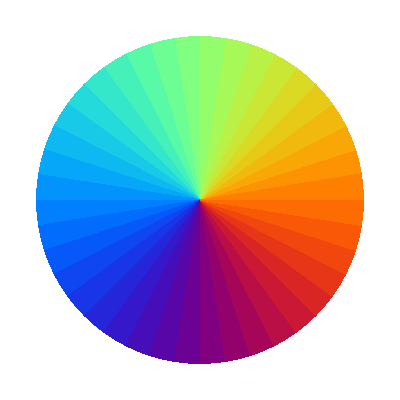

```mathematica
Graphics[Map[{RGBColor[Cos[#/2]^2,Sin[#]/2+0.5,1.0-Cos[#/2]^2],Disk[{0,0},1,{#,#+2π/39}]}&,Range[0,2π,2π/40]]]
```